```mathematica
Needs["ErrorBarPlots`"]
```

## Bosted fit

```mathematica
Q2=2.038
z=Sqrt[Q2]
tau=Q2/(4*0.938^2)
GEbosted= 1/(1+0.62*z+0.68*z^2+2.80*z^3+0.83*z^4)
GMbosted=2.7972*(1/(1+0.35*z+2.44*z^2+0.50*z^3+1.04*z^4+0.34*z^5))
Rffbosted=2.7972*GEbosted/GMbosted
RffPT=1+(-0.12)*Q2
```

2.038

1.42759

0.57908

0.0672736

0.19612

0.9595

0.75544

```mathematica
deltabosted= ((2.7972*GEbosted)^2-(GMbosted*RffPT)^2)/(RffPT^2+tau*2.7972^2)
R2gammabosted=1+ ((2*deltabosted*(1-eps))/(GMbosted^2+(eps/tau)*GEbosted^2))
```

0.00263844

1+(0.00527688 (1-eps))/(0.0384632+0.00781539 eps)

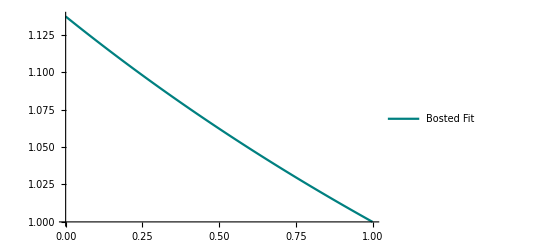

```mathematica
Pboosted=Plot[R2gammabosted,{eps,0,1},PlotStyle->{Blend[{Green,Blue}]},PlotLegends-> Placed[LineLegend[{"Bosted Fit"}],{0.7,0.95}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14]]
```

## Arrington Fit

```mathematica
x=Q2
GEarr=1/(1+3.226*x+1.508*x^2-0.3773*x^3+0.611*x^4-0.185*x^5)
GMarr=2.7972*(1/(1+3.19*x+1.355*x^2+0.151*x^3-1.14*10^-2*x^4+5.33*10^-4x^5-9*10^-6x^6))
Rffarrington= 2.7972*GEarr/GMarr
```

2.038

0.0681177

0.196588

0.969228

```mathematica
deltaarr =((2.7972*GEarr)^2-(GMarr*RffPT)^2)/(RffPT^2+tau*2.7972^2)
R2gammaarr=1+ ((2*deltaarr*(1-eps))/(GMarr^2+(eps/tau)*GEarr^2))
```

0.00279317

1+(0.00558634 (1-eps))/(0.0386468+0.00801274 eps)

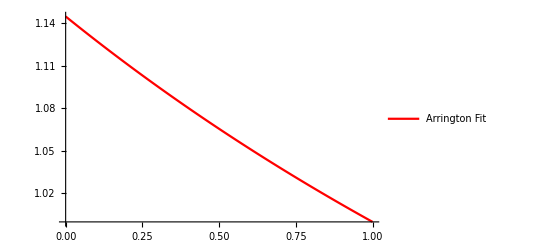

```mathematica
Parrington=Plot[R2gammaarr,{eps,0,1},PlotStyle->{Red},PlotLegends-> Placed[LineLegend[{"Arrington Fit"}],{0.7,0.85}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14]]
```

## Pade Model

```mathematica
a1=3.439
a2=-1.602
a3=0.068
b1=15.055
b2=48.061
b3=99.304
b4=0.012
b5=8.650
c1=-1.465
c2=1.260
c3=0.262
d1=9.627
d2=0.000
d3=0.000
d4=11.179
d5=13.245
```

3.439

-1.602

0.068

15.055

48.061

99.304

0.012

8.65

-1.465

1.26

0.262

9.627

0.

0.

11.179

13.245

0.0540132

0.201094

0.57908

0.75544

-0.0000492002

1-(0.0000984004 (1-eps))/(0.0404386+0.00503804 eps)

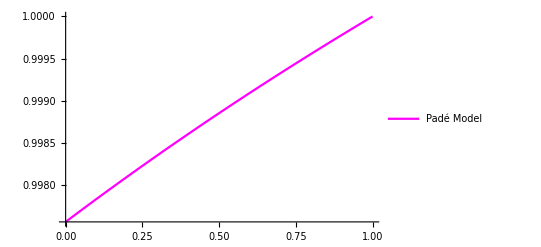

```mathematica
GEpade= (1+a1*tau+a2*tau^2+a3*tau^3)/(1+b1*tau+b2*tau^2+b3*tau^3+b4*tau^4+b5*tau^5)
GMpade= 2.7972*((1+c1*tau+c2*tau^2+c3*tau^3)/(1+d1*tau+d2*tau^2+d3*tau^3+d4*tau^4+d5*tau^5))
tau=Q2/(4*0.938^2)
RffPT=1-0.12*Q2
deltaBern=((2.7972*GEpade)^2-(GMpade*RffPT)^2)/(RffPT^2+tau*2.7972^2)
R2gammaBern=1+ ((2*deltaBern*(1-eps))/(GMpade^2+(eps/tau)*GEpade^2))
PltBernauer=Plot[R2gammaBern,{eps,0,1},PlotStyle->{Magenta},PlotLegends-> Placed[LineLegend[{"Padé Model"}],{0.73,0.75}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->16]]
```

## Standard Dipole Fit

0.0667549

0.186727

0.00293412

1+(0.00586825 (1-eps))/(0.0348669+0.00769534 eps)

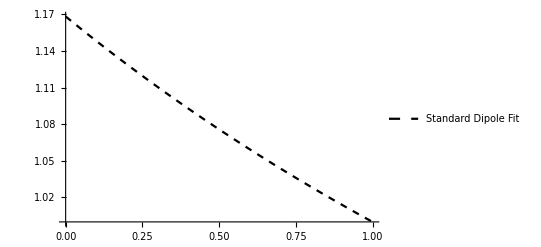

```mathematica
GEdip=1/(1+(Q2/0.71))^2
Gmdip=2.7972*GEdip
deltaDip=((2.7972*GEdip)^2-(Gmdip*RffPT)^2)/(RffPT^2+tau*2.7972^2)
R2gammaDip=1+ ((2*deltaDip*(1-eps))/(Gmdip^2+(eps/tau)*GEdip^2))
Pdipole=Plot[R2gammaDip,{eps,0,1},PlotStyle->{Black, Dashed},PlotLegends-> Placed[LineLegend[{"Standard Dipole Fit"}],{0.75,0.65}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14]]
```

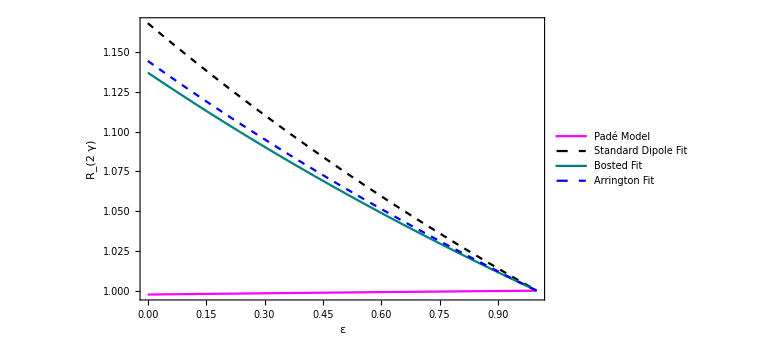

```mathematica
Show[PltBernauer,Pdipole,Pboosted,Parrington,PlotRange->All,Frame-> True,FrameTicks->All,FrameLabel->{Style["ε",Bold,18],Style["R_(2  γ)",Bold,18]},  ImageSize-> Large]
```

## Olympus Experiment

```mathematica
OLYMPUSdata=Import["F:\\Fahad Documents\\Dept. of Physics,SUST\\Study Materials\\4-2\\PROJECT PHY428-20220803T021501Z-001\\PROJECT PHY428\\Figures\\MATHEMATICA\\R_2gamma calculation\\OLYMPUS\\Olympus data 2017_Henderson.csv"]
```

{{Q^2,,varepsilon,R_{2\gamma},error(sys),error(stat),error(tatal)},{0.165,,0.978,0.9971,0.003,0.0036,0.00468615},{0.624,,0.898,0.992,0.0019,0.0045,0.00488467},{0.674,,0.887,0.9888,0.0021,0.0045,0.00496588},{0.724,,0.876,0.9897,0.0023,0.0045,0.00505371},{0.774,,0.865,0.9883,0.0026,0.0045,0.00519712},{0.824,,0.853,0.9879,0.0029,0.0045,0.0053535},{0.874,,0.841,0.9907,0.0032,0.0045,0.00552178},{0.924,1.10925,0.829,0.9919,0.0036,0.0045,0.00576281},{0.974,,0.816,0.995,0.0039,0.0045,0.00595483},{1.024,,0.803,0.9913,0.0043,0.0045,0.00622415},{1.074,,0.789,0.9905,0.0047,0.0045,0.00650692},{1.124,,0.775,0.9904,0.0052,0.0045,0.00687677},{1.174,,0.761,0.995,0.0057,0.0045,0.00726223},{1.246,,0.739,0.9945,0.0046,0.0045,0.00643506},{1.347,,0.708,0.9915,0.0054,0.0046,0.00709366},{1.447,,0.676,0.9842,0.0063,0.0046,0.00780064},{1.568,,0.635,1.0043,0.0063,0.0046,0.00780064},{1.718,,0.581,0.9968,0.0077,0.0046,0.00896939},{1.868,,0.524,0.9953,0.0095,0.0046,0.0105551},{2.038,,0.456,1.0089,0.0104,0.0046,0.0113719}}

```mathematica
TableForm[OLYMPUSdata]
```

Q^2 |  | varepsilon | R_{2\gamma} | error(sys) | error(stat) | error(tatal)
0.165 |  | 0.978 | 0.9971 | 0.003 | 0.0036 | 0.00468615
0.624 |  | 0.898 | 0.992 | 0.0019 | 0.0045 | 0.00488467
0.674 |  | 0.887 | 0.9888 | 0.0021 | 0.0045 | 0.00496588
0.724 |  | 0.876 | 0.9897 | 0.0023 | 0.0045 | 0.00505371
0.774 |  | 0.865 | 0.9883 | 0.0026 | 0.0045 | 0.00519712
0.824 |  | 0.853 | 0.9879 | 0.0029 | 0.0045 | 0.0053535
0.874 |  | 0.841 | 0.9907 | 0.0032 | 0.0045 | 0.00552178
0.924 | 1.10925 | 0.829 | 0.9919 | 0.0036 | 0.0045 | 0.00576281
0.974 |  | 0.816 | 0.995 | 0.0039 | 0.0045 | 0.00595483
1.024 |  | 0.803 | 0.9913 | 0.0043 | 0.0045 | 0.00622415
1.074 |  | 0.789 | 0.9905 | 0.0047 | 0.0045 | 0.00650692
1.124 |  | 0.775 | 0.9904 | 0.0052 | 0.0045 | 0.00687677
1.174 |  | 0.761 | 0.995 | 0.0057 | 0.0045 | 0.00726223
1.246 |  | 0.739 | 0.9945 | 0.0046 | 0.0045 | 0.00643506
1.347 |  | 0.708 | 0.9915 | 0.0054 | 0.0046 | 0.00709366
1.447 |  | 0.676 | 0.9842 | 0.0063 | 0.0046 | 0.00780064
1.568 |  | 0.635 | 1.0043 | 0.0063 | 0.0046 | 0.00780064
1.718 |  | 0.581 | 0.9968 | 0.0077 | 0.0046 | 0.00896939
1.868 |  | 0.524 | 0.9953 | 0.0095 | 0.0046 | 0.0105551
2.038 |  | 0.456 | 1.0089 | 0.0104 | 0.0046 | 0.0113719

```mathematica
Transpose[%118]
```

{{Q^2,0.165,0.624,0.674,0.724,0.774,0.824,0.874,0.924,0.974,1.024,1.074,1.124,1.174,1.246,1.347,1.447,1.568,1.718,1.868,2.038},{,,,,,,,,1.10925,,,,,,,,,,,,},{varepsilon,0.978,0.898,0.887,0.876,0.865,0.853,0.841,0.829,0.816,0.803,0.789,0.775,0.761,0.739,0.708,0.676,0.635,0.581,0.524,0.456},{R_{2\gamma},0.9971,0.992,0.9888,0.9897,0.9883,0.9879,0.9907,0.9919,0.995,0.9913,0.9905,0.9904,0.995,0.9945,0.9915,0.9842,1.0043,0.9968,0.9953,1.0089},{error(sys),0.003,0.0019,0.0021,0.0023,0.0026,0.0029,0.0032,0.0036,0.0039,0.0043,0.0047,0.0052,0.0057,0.0046,0.0054,0.0063,0.0063,0.0077,0.0095,0.0104},{error(stat),0.0036,0.0045,0.0045,0.0045,0.0045,0.0045,0.0045,0.0045,0.0045,0.0045,0.0045,0.0045,0.0045,0.0045,0.0046,0.0046,0.0046,0.0046,0.0046,0.0046},{error(tatal),0.00468615,0.00488467,0.00496588,0.00505371,0.00519712,0.0053535,0.00552178,0.00576281,0.00595483,0.00622415,0.00650692,0.00687677,0.00726223,0.00643506,0.00709366,0.00780064,0.00780064,0.00896939,0.0105551,0.0113719}}

```mathematica
epsdataC={0.978,0.898,0.887,0.876,0.865,0.853,0.841,0.829,0.816,0.803,0.789,0.775,0.761,0.739,0.708,0.676,0.635,0.581,0.524,0.456}
R2gammadataC={0.9971,0.992,0.9888,0.9897,0.9883,0.9879,0.9907,0.9919,0.995,0.9913,0.9905,0.9904,0.995,0.9945,0.9915,0.9842,1.0043,0.9968,0.9953,1.0089}
R2gammaerrorC={0.00468615,0.00488467,0.004965884,0.005053712,0.005197115,0.005353504,0.005521775,0.005762812,0.00595483,0.006224147,0.006506919,0.006876772,0.007262231,0.00643506,0.007093659,0.007800641,0.007800641,0.008969392,0.010555094,0.011371895}
dataCLAS=Transpose[{epsdataC, R2gammadataC}]
errorplotCLAS= Transpose[{epsdataC, R2gammadataC, R2gammaerrorC}]
```

{0.978,0.898,0.887,0.876,0.865,0.853,0.841,0.829,0.816,0.803,0.789,0.775,0.761,0.739,0.708,0.676,0.635,0.581,0.524,0.456}

{0.9971,0.992,0.9888,0.9897,0.9883,0.9879,0.9907,0.9919,0.995,0.9913,0.9905,0.9904,0.995,0.9945,0.9915,0.9842,1.0043,0.9968,0.9953,1.0089}

{0.00468615,0.00488467,0.00496588,0.00505371,0.00519712,0.0053535,0.00552178,0.00576281,0.00595483,0.00622415,0.00650692,0.00687677,0.00726223,0.00643506,0.00709366,0.00780064,0.00780064,0.00896939,0.0105551,0.0113719}

{{0.978,0.9971},{0.898,0.992},{0.887,0.9888},{0.876,0.9897},{0.865,0.9883},{0.853,0.9879},{0.841,0.9907},{0.829,0.9919},{0.816,0.995},{0.803,0.9913},{0.789,0.9905},{0.775,0.9904},{0.761,0.995},{0.739,0.9945},{0.708,0.9915},{0.676,0.9842},{0.635,1.0043},{0.581,0.9968},{0.524,0.9953},{0.456,1.0089}}

{{0.978,0.9971,0.00468615},{0.898,0.992,0.00488467},{0.887,0.9888,0.00496588},{0.876,0.9897,0.00505371},{0.865,0.9883,0.00519712},{0.853,0.9879,0.0053535},{0.841,0.9907,0.00552178},{0.829,0.9919,0.00576281},{0.816,0.995,0.00595483},{0.803,0.9913,0.00622415},{0.789,0.9905,0.00650692},{0.775,0.9904,0.00687677},{0.761,0.995,0.00726223},{0.739,0.9945,0.00643506},{0.708,0.9915,0.00709366},{0.676,0.9842,0.00780064},{0.635,1.0043,0.00780064},{0.581,0.9968,0.00896939},{0.524,0.9953,0.0105551},{0.456,1.0089,0.0113719}}

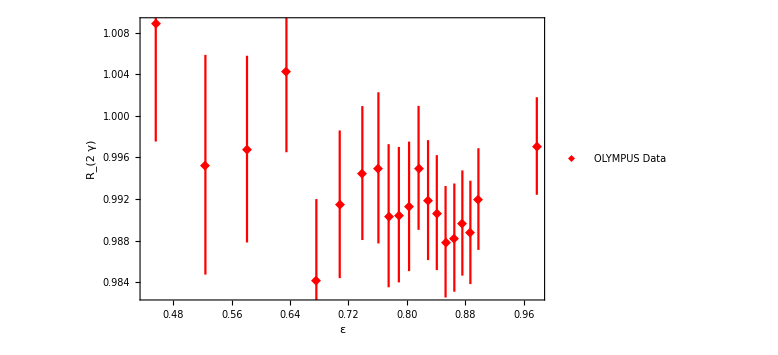

```mathematica
pltCLAS=ErrorListPlot[Table[{errorplotCLAS[[i,{1,2}]],ErrorBar[errorplotCLAS[[i,3]]]},{i,1,Length[errorplotCLAS]}], PlotStyle->Red,Joined->False,PlotMarkers->{"◆", Medium}, FrameLabel->{Style["ε",Bold,18],Style["R_(2  γ)",Bold,18]},PlotLegends-> Placed[LineLegend[{"OLYMPUS Data"}],{0.7,0.55}], Frame-> True,FrameTicks->All,LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14], ImageSize-> Large]
```

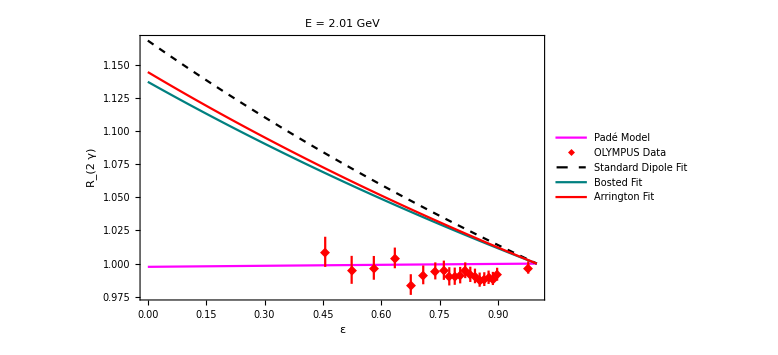

```mathematica
Show[PltBernauer,pltCLAS,Pdipole,Pboosted,Parrington,PlotRange->All,Frame-> True,FrameTicks->All,PlotLabel->Style["E = 2.01 GeV",Bold,Black],FrameLabel->{Style["ε",Bold,22,Black],Style["R_(2  γ)",Bold,20,Black]},Axes-> False,LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14], FrameTicksStyle-> Directive[Black,14],  ImageSize-> Large]
```